## Talbot re-imaging suppression

## 1D example

Want destructive interference from neighboring spots in the Talbot plane (spoiler, this won’t work, because the Talbot plane is where the field is reimaged, by definition).

```mathematica
Clear[λ,k,d, a]
```

```mathematica
k = (2 π)/λ; zT = (2 d^2)/λ; (*zT is Talbot length. d is the field period in transverse plane*)
```

```mathematica
Solve[k √(zT^2+d^2)-k zT == (2n+1) π, d](*n any integer*)
```

{{d→-(ⅈ (1+2 n) λ)/(√(4+16 n))},{d→(ⅈ (1+2 n) λ)/(√(4+16 n))}}

```mathematica
a = 0.0001;λ = 8.25*^-7;d=4.3a;
```

Get deviations our chosen grid period d, in units a:

```mathematica
Table[Re[(d-(-(ⅈ (1+2 n) λ)/(√(4+16 n))))/a],{n,Range[-1000000,-100000,100000]}]
```

{0.175002,0.386683,0.61049,0.848779,1.10479,1.38319,1.69112,2.04065,2.45525,2.99557}

Negative n does not correspond to a physically meaningful result, because the LHS side of the equation is always positive for physical situations.

Try getting constructive interference:

```mathematica
Solve[k √(z^2+d^2)-k z == 2n π, d](*n any integer*)
```

{{d→-(2 √π √(n^2 π+k n z))/k},{d→(2 √π √(n^2 π+k n z))/k}}

```mathematica
Solve[(2 √π √(n^2 π+k n z))/k==d,z]
```

{{z→(d^2 k^2-4 n^2 π^2)/(4 k n π)}}

Rearranging, 4n z= (2 d^2)/λ- 2 n^2 λ. The first term is clearly the Talbot length, even if the rest is not immediately decipherable.

## 2D example

Get destructive interference from next-to-nearest neighbor spots on a grid, so that they cancel each other rather than constructively interfere with the spot that is their mutual nearest neighbor.

```mathematica
Clear[λ, dx]
k = (2 π)/λ;zTx = (2 dx^2)/λ;
```

```mathematica
Solve[k(√(((2 dx^2)/λ)^2+(dx+δ)^2)-√(((2 dx^2)/λ)^2+dx^2))==(2n+1)π,δ]//FullSimplify
```

{{δ→-dx-1/2 √(4 dx^2+(1+2 n) λ (4 √(dx^2+(4 dx^4)/λ^2)+λ+2 n λ))},{δ→1/2 (-2 dx+√(4 dx^2+(1+2 n) λ (4 √(dx^2+(4 dx^4)/λ^2)+λ+2 n λ)))}}

```mathematica
Clear[n]
λ=8.25*^-7; dx=4.3*^-4; n=2;
Table[{1/2 (-2 dx+√(4 dx^2+(1+2 n) λ (4 √(dx^2+(4 dx^4)/λ^2)+λ+2 n λ))),(-dx-1/2 √(4 dx^2+(1+2 n) λ (4 √(dx^2+(4 dx^4)/λ^2)+λ+2 n λ)))},{n,0,10}]
```

{{0.000314782,-0.00117478},{0.000707674,-0.00156767},{0.00099615,-0.00185615},{0.00123539,-0.00209539},{0.00144433,-0.00230433},{0.00163221,-0.00249221},{0.00180435,-0.00266435},{0.00196415,-0.00282415},{0.00211392,-0.00297392},{0.00225536,-0.00311536},{0.00238971,-0.00324971}}

-0.00043-1/2 √(7.396×10^-7+8.25×10^-7 (1.79297+1.65×10^-6 n) (1+2 n))

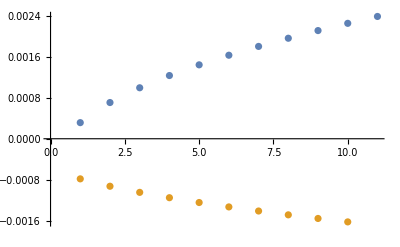

```mathematica
ListPlot[{Table[1/2 (-0.00086+√(7.396*^-7+8.25*^-7 (1.7929713469695072+1.65*^-6 n) (1+2 n))), {n, 0,10}],Table[1/2 (-0.00043-1/2 √(7.396*^-7+8.25*^-7 (1.7929713469695072+1.65*^-6 n) (1+2 n))), {n, 1,10}]}]
```

Next-to-nearest neighbors:

```mathematica
Clear[λ, d,n]
k = (2 π)/λ;zT = (2 d^2)/λ;
```

```mathematica
k(√(zT^2+(√2 d)^2)-zT)
```

3.14159

```mathematica
Clear[λ, d,n]
k = (2 π)/λ;zT = (2 d^2)/λ;
```

```mathematica
k(√(zT^2+(2d)^2)-zT)//Simplify
```

(-4 d^2 π+4 π √(d^2+d^4/λ^2) λ)/λ^2

```mathematica
Solve[k(√(zT^2+(2d+δ)^2)-zT)==(2n+1)π,δ]
```

{{δ→1/2 (-4 d-√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))},{δ→1/2 (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))}}

```mathematica
λ=8.25*^-7; d=4.3*^-4;
```

```mathematica
k(√(zT^2+(2d+δ)^2)-zT)
```

```mathematica
(6.283179525214146/k)
```

8.24999×10^-7

```mathematica
Solve[k(√(zT^2+(2d+δ)^2)-zT)==(2 n + 1)π, δ]
```

{{δ→1/2 (-4 d-√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))},{δ→1/2 (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))}}

```mathematica
λ=8.25*^-7; d=4.3*^-4;
```

```mathematica
Table[{1/2 (-4 d-√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2)),1/2 (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))},{n,0,10}]
```

{{-0.00146811,-0.000251888},{-0.00191328,0.000193281},{-0.00221978,0.000499781},{-0.00246892,0.000748915},{-0.00268434,0.000964339},{-0.00287688,0.00115688},{-0.00305258,0.00133258},{-0.00321522,0.00149522},{-0.00336732,0.00164732},{-0.00351071,0.00179071},{-0.00364673,0.00192673}}

```mathematica
0.0002/d
```

0.465116

```mathematica
Clear[λ,d]
```

```mathematica
Solve[k(√(zT^2+(d+δ)^2)-zT)==(2 n + 1)π, δ]
```

{{δ→1/2 (-2 d-√(4 zT λ+8 n zT λ+λ^2+4 n λ^2+4 n^2 λ^2))},{δ→1/2 (-2 d+√(4 zT λ+8 n zT λ+λ^2+4 n λ^2+4 n^2 λ^2))}}

```mathematica
Table[{1/2 (-2 d-√(4 zT λ+8 n zT λ+λ^2+4 n λ^2+4 n^2 λ^2)),1/2 (-2 d+√(4 zT λ+8 n zT λ+λ^2+4 n λ^2+4 n^2 λ^2))},{n,0,10}]
```

{{-0.00103811,0.000178112},{-0.00148328,0.000623281},{-0.00178978,0.000929781},{-0.00203892,0.00117892},{-0.00225434,0.00139434},{-0.00244688,0.00158688},{-0.00262258,0.00176258},{-0.00278522,0.00192522},{-0.00293732,0.00207732},{-0.00308071,0.00222071},{-0.00321673,0.00235673}}

```mathematica
0.0003/d
```

0.697674

```mathematica
0.000178/d
```

0.413953

```mathematica
(1.5707959655021742/k)
```

2.0625×10^-7

```mathematica
{zT,d, λ}
```

{0.448242,0.00043,8.25×10^-7}

```mathematica
Table[{1/2 (-4 d-√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2)), (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))}, {n,0,10}]
```

{{-0.00146811,-0.000503776},{-0.00191328,0.000386563},{-0.00221978,0.000999562},{-0.00246892,0.00149783},{-0.00268434,0.00192868},{-0.00287688,0.00231377},{-0.00305258,0.00266517},{-0.00321522,0.00299043},{-0.00336732,0.00329464},{-0.00351071,0.00358142},{-0.00364673,0.00385346}}

```mathematica
-2 √2 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2)/.n-> 0
```

```mathematica
nn = 1000;
```

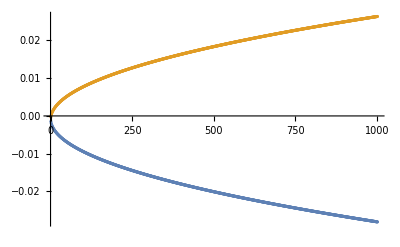

```mathematica
ListPlot[{Table[1/2 (-4 d-√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2)),{n,0,nn}],Table[1/2 (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2)), {n,0,nn}]}]
```

```mathematica
1/2 (-4 d+√(8 d^2+16 d^2 n+λ^2+4 n λ^2+4 n^2 λ^2))/.n-> 1
```

0.000193281